# Лабораторная работа №8

## Шульжик Дмитрий

## 4 курс 1 группа

```mathematica
k=17;
alpha = 0.3*k;
h = 0.4;
phi[x_,y_]:=(alpha^2+1)*x+(1-alpha)*y
psi[x_,y_]:=(1- alpha)*x^2+alpha*y^2+2*alpha
gamma[x_,y_]:=Sqrt[4-y^2]-Abs[x] ;
```

```mathematica
xk=# h&/@Range[-5,5];
yk = # h&/@Range[-5,5];
```

```mathematica
Flatten[Outer[{#1, #2}&, xk, yk], 1];
set=Select[%, (#⟦1⟧)^2+(#⟦2⟧)^2<=4&];
```

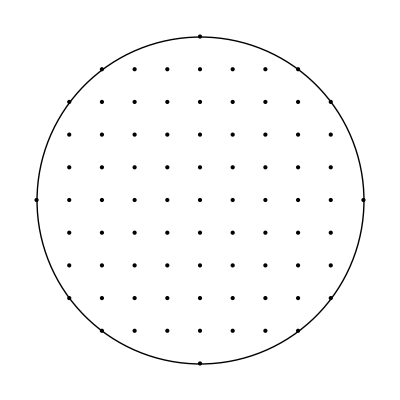

```mathematica
Graphics[{Point/@set, Circle[{0,0},2]}]
```

```mathematica
variables = Subscript[u, Round[#[[1]]/h], Round[#[[2]]/h]]&/@set;
```

```mathematica
conditions={
Subscript[u, 0, 5]==psi[xk[[6]],yk[[11]] ],
Subscript[u, 5, 0]==psi[xk[[11]],yk[[6]] ],
Subscript[u, 0, -5]==psi[xk[[6]],yk[[1]] ],
Subscript[u, -5, 0]==psi[xk[[1]],yk[[6]] ],
Subscript[u, 1, 4]==(h*psi[xk[[7]],yk[[10]]+gamma[xk[[7]],yk[[10]]]]+gamma[xk[[7]],yk[[10]]] Subscript[u, 1,3])/(h+gamma[xk[[7]],yk[[10]]]),
Subscript[u, 2, 4]==(h*psi[xk[[8]],yk[[10]]+gamma[xk[[8]],yk[[10]]]]+gamma[xk[[8]],yk[[10]]] Subscript[u, 2,3])/(h+gamma[xk[[7]],yk[[10]]]),
Subscript[u, 4, 1]==(h*psi[xk[[10]],yk[[7]]+gamma[xk[[10]],yk[[7]]]]+gamma[xk[[10]],yk[[7]]] Subscript[u, 3,1])/(h+gamma[xk[[10]],yk[[7]]]),
Subscript[u, 4, 2]==(h*psi[xk[[10]],yk[[8]]+gamma[xk[[10]],yk[[8]]]]+gamma[xk[[10]],yk[[8]]] Subscript[u, 3,2])/(h+gamma[xk[[10]],yk[[8]]]),

Subscript[u, -1, 4]==(h*psi[xk[[5]],yk[[10]]+gamma[xk[[5]],yk[[10]]]]+gamma[xk[[5]],yk[[10]]] Subscript[u, -1,3])/(h+gamma[xk[[5]],yk[[10]]]),
Subscript[u, -2, 4]==(h*psi[xk[[4]],yk[[10]]+gamma[xk[[4]],yk[[10]]]]+gamma[xk[[4]],yk[[10]]] Subscript[u, -2,3])/(h+gamma[xk[[4]],yk[[10]]]),
Subscript[u, -4, 1]==(h*psi[xk[[2]],yk[[7]]+gamma[xk[[2]],yk[[7]]]]+gamma[xk[[2]],yk[[7]]] Subscript[u, -3,1])/(h+gamma[xk[[2]],yk[[7]]]),
Subscript[u, -4, 2]==(h*psi[xk[[2]],yk[[8]]+gamma[xk[[2]],yk[[8]]]]+gamma[xk[[2]],yk[[8]]] Subscript[u, -3,2])/(h+gamma[xk[[2]],yk[[8]]]),

Subscript[u, 1, -4]==(h*psi[xk[[7]],yk[[2]]+gamma[xk[[7]],yk[[2]]]]+gamma[xk[[7]],yk[[2]]] Subscript[u, 1,-3])/(h+gamma[xk[[7]],yk[[2]]]),
Subscript[u, 2, -4]==(h*psi[xk[[8]],yk[[2]]+gamma[xk[[8]],yk[[2]]]]+gamma[xk[[8]],yk[[2]]] Subscript[u, 2,-3])/(h+gamma[xk[[8]],yk[[2]]]),
Subscript[u, 4, -1]==(h*psi[xk[[10]],yk[[5]]+gamma[xk[[10]],yk[[5]]]]+gamma[xk[[10]],yk[[5]]] Subscript[u, 3,-1])/(h+gamma[xk[[10]],yk[[5]]]),
Subscript[u, 4, -2]==(h*psi[xk[[10]],yk[[4]]+gamma[xk[[10]],yk[[4]]]]+gamma[xk[[10]],yk[[4]]] Subscript[u, 3,-2])/(h+gamma[xk[[10]],yk[[4]]]),

Subscript[u, -1, -4]==(h*psi[xk[[5]],yk[[2]]+gamma[xk[[5]],yk[[2]]]]+gamma[xk[[5]],yk[[2]]] Subscript[u, -1,-3])/(h+gamma[xk[[5]],yk[[2]]]),
Subscript[u, -2, -4]==(h*psi[xk[[4]],yk[[2]]+gamma[xk[[4]],yk[[2]]]]+gamma[xk[[4]],yk[[2]]] Subscript[u, -2,-3])/(h+gamma[xk[[4]],yk[[2]]]),
Subscript[u, -4, -1]==(h*psi[xk[[2]],yk[[5]]+gamma[xk[[2]],yk[[5]]]]+gamma[xk[[2]],yk[[5]]] Subscript[u, -3,-1])/(h+gamma[xk[[2]],yk[[5]]]),
Subscript[u, -4, -2]==(h*psi[xk[[2]],yk[[4]]+gamma[xk[[2]],yk[[4]]]]+gamma[xk[[2]],yk[[4]]] Subscript[u, -3,-2])/(h+gamma[xk[[2]],yk[[4]]]),

Subscript[u, 4, 3]==psi[xk[[10]],yk[[9]] ],
Subscript[u, 3, 4]==psi[xk[[9]],yk[[10]] ],
Subscript[u, -4, 3]==psi[xk[[2]],yk[[9]] ],
Subscript[u, -3, 4]==psi[xk[[3]],yk[[2]] ],
Subscript[u, 4, -3]==psi[xk[[10]],yk[[3]] ],
Subscript[u, 3, -4]==psi[xk[[9]],yk[[2]] ],
Subscript[u, -4, -3]==psi[xk[[2]],yk[[3]] ],
Subscript[u, -3, -4]==psi[xk[[3]],yk[[2]] ]}
```

{u_(0,5)==30.6,u_(5,0)==-6.2,u_(0,-5)==30.6,u_(-5,0)==-6.2,u_(1,4)==0.833333 (15.568+0.8 u_(1,3)),u_(2,4)==0.833333 (11.1904+0.4 u_(2,3)),u_(4,1)==1.3165 (1.05864+0.359592 u_(3,1)),u_(4,2)==1.5797 (2.05859+0.23303 u_(3,2)),u_(-1,4)==0.833333 (15.568+0.8 u_(-1,3)),u_(-2,4)==1.25 (11.1904+0.4 u_(-2,3)),u_(-4,1)==1.3165 (1.05864+0.359592 u_(-3,1)),u_(-4,2)==1.5797 (2.05859+0.23303 u_(-3,2)),u_(1,-4)==0.833333 (5.1232+0.8 u_(1,-3)),u_(2,-4)==1.25 (5.968+0.4 u_(2,-3)),u_(4,-1)==1.3165 (-0.115069+0.359592 u_(3,-1)),u_(4,-2)==1.5797 (0.537368+0.23303 u_(3,-2)),u_(-1,-4)==0.833333 (5.1232+0.8 u_(-1,-3)),u_(-2,-4)==1.25 (5.968+0.4 u_(-2,-3)),u_(-4,-1)==1.3165 (-0.115069+0.359592 u_(-3,-1)),u_(-4,-2)==1.5797 (0.537368+0.23303 u_(-3,-2)),u_(4,3)==7.048,u_(3,4)==17.352,u_(-4,3)==7.048,u_(-3,4)==17.352,u_(4,-3)==7.048,u_(3,-4)==17.352,u_(-4,-3)==7.048,u_(-3,-4)==17.352}

```mathematica
equations=DeleteCases[Flatten[Table[If[Intersection[variables, {Subscript[u, m+1,n], Subscript[u, m,n], Subscript[u, m-1,n],Subscript[u, m,n+1], Subscript[u, m,n-1] }]==Sort[{Subscript[u, m+1,n], Subscript[u, m,n], Subscript[u, m-1,n],Subscript[u, m,n+1], Subscript[u, m,n-1]}],(Subscript[u, m+1,n]-2 Subscript[u, m,n]+Subscript[u, m-1,n])/h^2+(Subscript[u, m,n+1]-2 Subscript[u, m,n]+Subscript[u, m,n-1])/h^2==phi[xk[[m+5]],yk[[n+5]]]], {m, -4, 4}, {n, -4, 4}], 1], Null];
```

```mathematica
Scan[Print, Join[equations, conditions]]
```

6.25 (u_(-4,-1)-2 u_(-4,0)+u_(-4,1))+6.25 (u_(-5,0)-2 u_(-4,0)+u_(-3,0))==-52.38

6.25 (u_(-3,-4)-2 u_(-3,-3)+u_(-3,-2))+6.25 (u_(-4,-3)-2 u_(-3,-3)+u_(-2,-3))==-36.656

6.25 (u_(-3,-3)-2 u_(-3,-2)+u_(-3,-1))+6.25 (u_(-4,-2)-2 u_(-3,-2)+u_(-2,-2))==-38.296

6.25 (u_(-3,-2)-2 u_(-3,-1)+u_(-3,0))+6.25 (u_(-4,-1)-2 u_(-3,-1)+u_(-2,-1))==-39.936

6.25 (u_(-3,-1)-2 u_(-3,0)+u_(-3,1))+6.25 (u_(-4,0)-2 u_(-3,0)+u_(-2,0))==-41.576

6.25 (u_(-3,0)-2 u_(-3,1)+u_(-3,2))+6.25 (u_(-4,1)-2 u_(-3,1)+u_(-2,1))==-43.216

6.25 (u_(-3,1)-2 u_(-3,2)+u_(-3,3))+6.25 (u_(-4,2)-2 u_(-3,2)+u_(-2,2))==-44.856

6.25 (u_(-3,2)-2 u_(-3,3)+u_(-3,4))+6.25 (u_(-4,3)-2 u_(-3,3)+u_(-2,3))==-46.496

6.25 (u_(-2,-4)-2 u_(-2,-3)+u_(-2,-2))+6.25 (u_(-3,-3)-2 u_(-2,-3)+u_(-1,-3))==-25.852

6.25 (u_(-2,-3)-2 u_(-2,-2)+u_(-2,-1))+6.25 (u_(-3,-2)-2 u_(-2,-2)+u_(-1,-2))==-27.492

6.25 (u_(-2,-2)-2 u_(-2,-1)+u_(-2,0))+6.25 (u_(-3,-1)-2 u_(-2,-1)+u_(-1,-1))==-29.132

6.25 (u_(-2,-1)-2 u_(-2,0)+u_(-2,1))+6.25 (u_(-3,0)-2 u_(-2,0)+u_(-1,0))==-30.772

6.25 (u_(-2,0)-2 u_(-2,1)+u_(-2,2))+6.25 (u_(-3,1)-2 u_(-2,1)+u_(-1,1))==-32.412

6.25 (u_(-2,1)-2 u_(-2,2)+u_(-2,3))+6.25 (u_(-3,2)-2 u_(-2,2)+u_(-1,2))==-34.052

6.25 (u_(-2,2)-2 u_(-2,3)+u_(-2,4))+6.25 (u_(-3,3)-2 u_(-2,3)+u_(-1,3))==-35.692

6.25 (u_(-1,-4)-2 u_(-1,-3)+u_(-1,-2))+6.25 (u_(-2,-3)-2 u_(-1,-3)+u_(0,-3))==-15.048

6.25 (u_(-1,-3)-2 u_(-1,-2)+u_(-1,-1))+6.25 (u_(-2,-2)-2 u_(-1,-2)+u_(0,-2))==-16.688

6.25 (u_(-1,-2)-2 u_(-1,-1)+u_(-1,0))+6.25 (u_(-2,-1)-2 u_(-1,-1)+u_(0,-1))==-18.328

6.25 (u_(-1,-1)-2 u_(-1,0)+u_(-1,1))+6.25 (u_(-2,0)-2 u_(-1,0)+u_(0,0))==-19.968

6.25 (u_(-1,0)-2 u_(-1,1)+u_(-1,2))+6.25 (u_(-2,1)-2 u_(-1,1)+u_(0,1))==-21.608

6.25 (u_(-1,1)-2 u_(-1,2)+u_(-1,3))+6.25 (u_(-2,2)-2 u_(-1,2)+u_(0,2))==-23.248

6.25 (u_(-1,2)-2 u_(-1,3)+u_(-1,4))+6.25 (u_(-2,3)-2 u_(-1,3)+u_(0,3))==-24.888

6.25 (u_(0,-5)-2 u_(0,-4)+u_(0,-3))+6.25 (u_(-1,-4)-2 u_(0,-4)+u_(1,-4))==-2.604

6.25 (u_(0,-4)-2 u_(0,-3)+u_(0,-2))+6.25 (u_(-1,-3)-2 u_(0,-3)+u_(1,-3))==-4.244

6.25 (u_(0,-3)-2 u_(0,-2)+u_(0,-1))+6.25 (u_(-1,-2)-2 u_(0,-2)+u_(1,-2))==-5.884

6.25 (u_(0,-2)-2 u_(0,-1)+u_(0,0))+6.25 (u_(-1,-1)-2 u_(0,-1)+u_(1,-1))==-7.524

6.25 (u_(0,-1)-2 u_(0,0)+u_(0,1))+6.25 (u_(-1,0)-2 u_(0,0)+u_(1,0))==-9.164

6.25 (u_(0,0)-2 u_(0,1)+u_(0,2))+6.25 (u_(-1,1)-2 u_(0,1)+u_(1,1))==-10.804

6.25 (u_(0,1)-2 u_(0,2)+u_(0,3))+6.25 (u_(-1,2)-2 u_(0,2)+u_(1,2))==-12.444

6.25 (u_(0,2)-2 u_(0,3)+u_(0,4))+6.25 (u_(-1,3)-2 u_(0,3)+u_(1,3))==-14.084

6.25 (u_(0,3)-2 u_(0,4)+u_(0,5))+6.25 (u_(-1,4)-2 u_(0,4)+u_(1,4))==-15.724

6.25 (u_(1,-4)-2 u_(1,-3)+u_(1,-2))+6.25 (u_(0,-3)-2 u_(1,-3)+u_(2,-3))==6.56

6.25 (u_(1,-3)-2 u_(1,-2)+u_(1,-1))+6.25 (u_(0,-2)-2 u_(1,-2)+u_(2,-2))==4.92

6.25 (u_(1,-2)-2 u_(1,-1)+u_(1,0))+6.25 (u_(0,-1)-2 u_(1,-1)+u_(2,-1))==3.28

6.25 (u_(1,-1)-2 u_(1,0)+u_(1,1))+6.25 (u_(0,0)-2 u_(1,0)+u_(2,0))==1.64

6.25 (u_(1,0)-2 u_(1,1)+u_(1,2))+6.25 (u_(0,1)-2 u_(1,1)+u_(2,1))==0.

6.25 (u_(1,1)-2 u_(1,2)+u_(1,3))+6.25 (u_(0,2)-2 u_(1,2)+u_(2,2))==-1.64

6.25 (u_(1,2)-2 u_(1,3)+u_(1,4))+6.25 (u_(0,3)-2 u_(1,3)+u_(2,3))==-3.28

6.25 (u_(2,-4)-2 u_(2,-3)+u_(2,-2))+6.25 (u_(1,-3)-2 u_(2,-3)+u_(3,-3))==17.364

6.25 (u_(2,-3)-2 u_(2,-2)+u_(2,-1))+6.25 (u_(1,-2)-2 u_(2,-2)+u_(3,-2))==15.724

6.25 (u_(2,-2)-2 u_(2,-1)+u_(2,0))+6.25 (u_(1,-1)-2 u_(2,-1)+u_(3,-1))==14.084

6.25 (u_(2,-1)-2 u_(2,0)+u_(2,1))+6.25 (u_(1,0)-2 u_(2,0)+u_(3,0))==12.444

6.25 (u_(2,0)-2 u_(2,1)+u_(2,2))+6.25 (u_(1,1)-2 u_(2,1)+u_(3,1))==10.804

6.25 (u_(2,1)-2 u_(2,2)+u_(2,3))+6.25 (u_(1,2)-2 u_(2,2)+u_(3,2))==9.164

6.25 (u_(2,2)-2 u_(2,3)+u_(2,4))+6.25 (u_(1,3)-2 u_(2,3)+u_(3,3))==7.524

6.25 (u_(3,-4)-2 u_(3,-3)+u_(3,-2))+6.25 (u_(2,-3)-2 u_(3,-3)+u_(4,-3))==28.168

6.25 (u_(3,-3)-2 u_(3,-2)+u_(3,-1))+6.25 (u_(2,-2)-2 u_(3,-2)+u_(4,-2))==26.528

6.25 (u_(3,-2)-2 u_(3,-1)+u_(3,0))+6.25 (u_(2,-1)-2 u_(3,-1)+u_(4,-1))==24.888

6.25 (u_(3,-1)-2 u_(3,0)+u_(3,1))+6.25 (u_(2,0)-2 u_(3,0)+u_(4,0))==23.248

6.25 (u_(3,0)-2 u_(3,1)+u_(3,2))+6.25 (u_(2,1)-2 u_(3,1)+u_(4,1))==21.608

6.25 (u_(3,1)-2 u_(3,2)+u_(3,3))+6.25 (u_(2,2)-2 u_(3,2)+u_(4,2))==19.968

6.25 (u_(3,2)-2 u_(3,3)+u_(3,4))+6.25 (u_(2,3)-2 u_(3,3)+u_(4,3))==18.328

6.25 (u_(4,-1)-2 u_(4,0)+u_(4,1))+6.25 (u_(3,0)-2 u_(4,0)+u_(5,0))==34.052

u_(0,5)==30.6

u_(5,0)==-6.2

u_(0,-5)==30.6

u_(-5,0)==-6.2

u_(1,4)==0.833333 (15.568+0.8 u_(1,3))

u_(2,4)==0.833333 (11.1904+0.4 u_(2,3))

u_(4,1)==1.3165 (1.05864+0.359592 u_(3,1))

u_(4,2)==1.5797 (2.05859+0.23303 u_(3,2))

u_(-1,4)==0.833333 (15.568+0.8 u_(-1,3))

u_(-2,4)==1.25 (11.1904+0.4 u_(-2,3))

u_(-4,1)==1.3165 (1.05864+0.359592 u_(-3,1))

u_(-4,2)==1.5797 (2.05859+0.23303 u_(-3,2))

u_(1,-4)==0.833333 (5.1232+0.8 u_(1,-3))

u_(2,-4)==1.25 (5.968+0.4 u_(2,-3))

u_(4,-1)==1.3165 (-0.115069+0.359592 u_(3,-1))

u_(4,-2)==1.5797 (0.537368+0.23303 u_(3,-2))

u_(-1,-4)==0.833333 (5.1232+0.8 u_(-1,-3))

u_(-2,-4)==1.25 (5.968+0.4 u_(-2,-3))

u_(-4,-1)==1.3165 (-0.115069+0.359592 u_(-3,-1))

u_(-4,-2)==1.5797 (0.537368+0.23303 u_(-3,-2))

u_(4,3)==7.048

u_(3,4)==17.352

u_(-4,3)==7.048

u_(-3,4)==17.352

u_(4,-3)==7.048

u_(3,-4)==17.352

u_(-4,-3)==7.048

u_(-3,-4)==17.352

```mathematica
solutions=First@Solve[
Join[
equations,
conditions
], Subscript[u, Round[#⟦1⟧]/4, Round[#⟦2⟧]/4]&/@(10 set)];
```

```mathematica
U=Outer[{#1, #2}&, xk, yk];
```

```mathematica
U=U/.{p_, q_}:>If[p^2+q^2<=4, Subscript[u, Round[10 p]/4, Round[10 q]/4], ""];
```

```mathematica
U=U/.solutions;
```

```mathematica
Grid[Join[{Join[{"y_i/x_i"}, Range[-2., 2., h]]},MapThread[Prepend[#2, #1]&, {Range[-2., 2., h],U}]], Spacings->{1, 2}, Frame->{{True},{True}}]
```

y_i/x_i | -2. | -1.6 | -1.2 | -0.8 | -0.4 | 0. | 0.4 | 0.8 | 1.2 | 1.6 | 2.
-2. |  |  |  |  |  | -6.2 |  |  |  |  | 
-1.6 |  |  | 7.048 | 7.4979 | 9.13212 | 11.1276 | 11.9489 | 11.4653 | 7.048 |  | 
-1.2 |  | 17.352 | 17.1149 | 18.0622 | 19.6104 | 21.2488 | 22.2965 | 22.3117 | 20.5631 | 17.352 | 
-0.8 |  | 17.5263 | 20.1327 | 21.898 | 23.6089 | 25.3084 | 26.762 | 27.7451 | 28.1015 | 28.0387 | 
-0.4 |  | 17.506 | 19.8551 | 21.3896 | 22.9577 | 24.6902 | 26.5123 | 28.3566 | 30.3482 | 33.2055 | 
0. | 30.6 | 19.9129 | 17.9843 | 18.1775 | 19.2097 | 20.7875 | 22.783 | 25.1013 | 27.7472 | 30.5498 | 30.6
0.4 |  | 13.1445 | 13.3127 | 13.1849 | 13.7123 | 15.0009 | 17.0023 | 19.5275 | 22.736 | 28.1306 | 
0.8 |  | 12.4534 | 9.98688 | 8.3241 | 7.9786 | 8.76383 | 10.6977 | 13.0079 | 15.0138 | 14.3299 | 
1.2 |  | 17.352 | 8.63548 | 4.66193 | 3.36758 | 3.36915 | 5.74556 | 8.25898 | 11.1851 | 17.352 | 
1.6 |  |  | 7.048 | 2.56502 | 1.44273 | -0.680698 | 4.11365 | 6.29225 | 7.048 |  | 
2. |  |  |  |  |  | -6.2 |  |  |  |  |